```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\InhibitorT.xlsx"]
```

```mathematica
data={{9.,-0.0014679904142416906},{18.,0.0018039484194910455},{27.,0.005229259386055004},{36.,0.007657651489216019},{45.,0.010009357525961422}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\Inhibitor1T.xlsx"]
```

```mathematica
data1={{9.,-0.0019792308570124304},{18.,-0.00008764121876069238},{27.,0.0025196850393700817},{36.,0.004641332876868654},{45.,0.0059961200502111145}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\Inhibitor2T.xlsx"]
```

```mathematica
data2={{9.,-0.0022348510783978003},{18.,0.00006573091407052939},{27.,0.0023918749286773963},{36.,0.004641332876868654},{45.,0.00678854273650576}};
a1=LinearModelFit[data,x,x]
```

```mathematica
b1=LinearModelFit[data1,x,x]
```

```mathematica
c1=LinearModelFit[data2,x,x]
```

```mathematica
a=ListPlot[data];
b=ListPlot[data1];
```

```mathematica
c=ListPlot[data2];
```

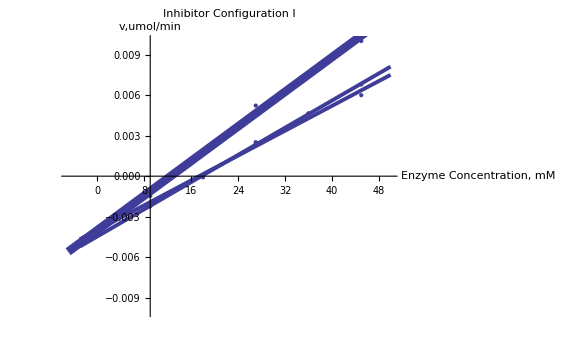

Plot::nonopt: Options expected (instead of {y, 0, 0.01}) beyond position 3 in Plot[a1, {x, 0, 50}, {y, 0, 0.01}]. An option must be a rule or a list of rules.

```mathematica
Show[a,b,c,Plot[a1[x],{x,-5,50},PlotStyle->{Thickness[0.011]}],Plot[b1[x],{x,-3,50},PlotStyle->{Thickness[0.005]}],Plot[c1[x],{x,-3,50},PlotStyle->{Thickness[0.005]}],PlotLabel->"Inhibitor Configuration I",AxesLabel->{"Enzyme Concentration, ug/mL","v,umol/min"},PlotRange->{-.01,0.01}]
```